# Mixed Graph Algorithm

Author Name

Abstract

## Section

XXXX:

## Eulerian Graph

```mathematica
RandomMixedGraph[g_?GraphQ]:=
```

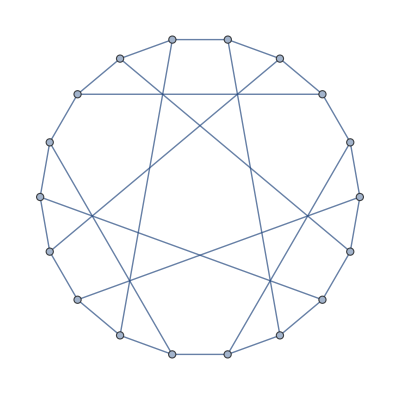

```mathematica
GraphData["PappusGraph"]
```

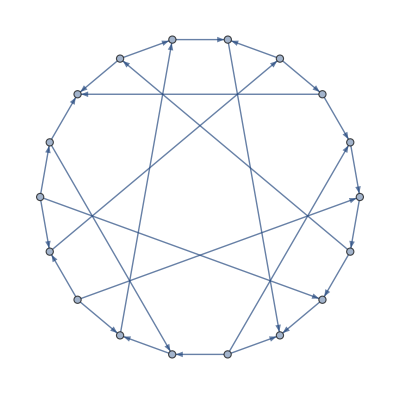

```mathematica
DirectedGraph[GraphData["PappusGraph"],"Random"]
```

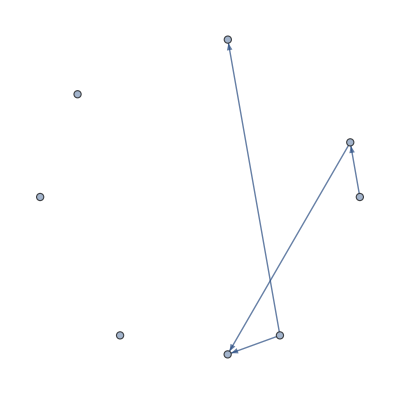

```mathematica
Subgraph[DirectedGraph[GraphData["PappusGraph"],"Random"],RandomSample[Range[VertexCount[GraphData["PappusGraph"]]],8]]
```

```mathematica
GraphUnion[GraphData["PappusGraph"],TakeLargest[#,1]&@ConnectedComponents@Subgraph[DirectedGraph[GraphData["PappusGraph"],"Random"],RandomSample[Range[VertexCount[GraphData["PappusGraph"]]],8]]]
```

GraphUnion[-Graphics-,Graph[TakeLargest[{{2},{17},{14},{5},{6},{18},{7},{10}},1]]]

```mathematica
FindGraphIsomorphism[GraphUnion[GraphData["PappusGraph"],Subgraph[DirectedGraph[GraphData["PappusGraph"],"Random"],RandomSample[Range[VertexCount[GraphData["PappusGraph"]]],8]]],GraphData["PappusGraph"]]
```

{}

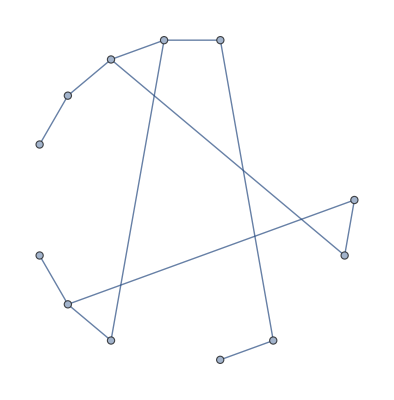

```mathematica
Subgraph[GraphData["PappusGraph"],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]
```

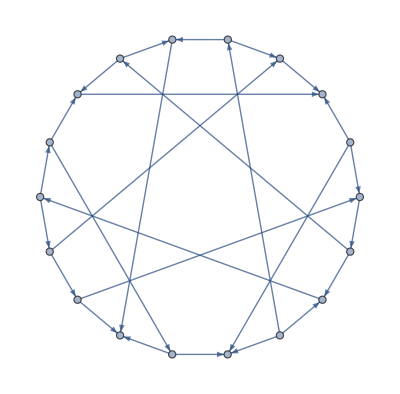

```mathematica
DirectedGraph[GraphData["PappusGraph"],"Random"]
```

```mathematica
GraphUnion[DirectedGraph[GraphData["PappusGraph"],"Random"],Subgraph[GraphData["PappusGraph"],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]]
```

-Graphics-

```mathematica
GraphSum[DirectedGraph[GraphData["PappusGraph"],"Random"],Subgraph[GraphData["PappusGraph"],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]]
```

-Graphics-

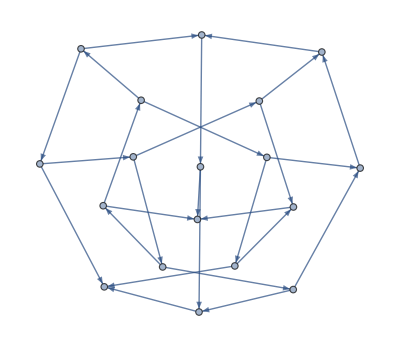

```mathematica
GraphDifference[DirectedGraph[GraphData["PappusGraph"],"Random"],Subgraph[GraphData["PappusGraph"],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]]
```

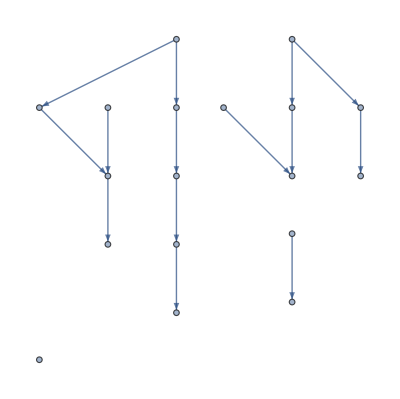

```mathematica
GraphDifference[GraphDifference[DirectedGraph[GraphData["PappusGraph"],"Random"],Subgraph[GraphData["PappusGraph"],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]],DirectedGraph[GraphData["PappusGraph"],"Random"]]
```

```mathematica
GraphSum[GraphDifference[GraphDifference[DirectedGraph[GraphData["PappusGraph"],"Random"],Subgraph[GraphData["PappusGraph"],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]],DirectedGraph[GraphData["PappusGraph"],"Random"]],GraphData["PappusGraph"]]
```

-Graphics-

```mathematica
RandomSample[VertexList[GraphData["PappusGraph"]]]
```

{10,12,18,2,11,5,16,7,9,8,13,1,3,4,15,17,6,14}

```mathematica
RandomSample[EdgeList[GraphData["PappusGraph"]],8]
```

{14<->17,10<->13,15<->18,3<->6,17<->18,11<->14,3<->18,2<->16}

```mathematica
RandomSample[EdgeList[GraphData["PappusGraph"]],8]/.{u_<->v_->DirectedEdge[u,v]}
```

{6->9,14->17,10->14,1->15,17->18,3->18,11->12,1->16}

```mathematica
Complement[EdgeList[GraphData["PappusGraph"]],RandomSample[EdgeList[GraphData["PappusGraph"]],8]]
```

{1<->4,1<->15,1<->16,2<->16,3<->6,3<->7,3<->18,4<->8,5<->6,5<->8,6<->9,7<->10,8<->11,9<->12,9<->13,10<->14,11<->14,12<->15,14<->17}

```mathematica
Join[Complement[EdgeList[GraphData["PappusGraph"]],RandomSample[EdgeList[GraphData["PappusGraph"]],8]],RandomSample[EdgeList[GraphData["PappusGraph"]],8]/.{u_<->v_->DirectedEdge[u,v]}]
```

{1<->16,2<->16,2<->17,3<->6,3<->18,4<->7,4<->8,6<->9,7<->10,8<->11,9<->12,9<->13,10<->13,11<->12,12<->15,13<->16,14<->17,15<->18,17<->18,10->13,11->12,11->14,2->17,8->11,4->8,6->9,14->17}

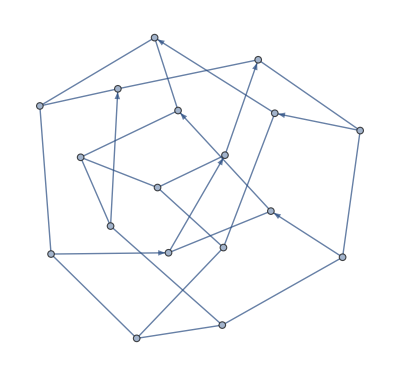

```mathematica
Graph[Join[Complement[EdgeList[GraphData["PappusGraph"]],BlockRandom@RandomSample[EdgeList[GraphData["PappusGraph"]],8]],RandomSample[EdgeList[GraphData["PappusGraph"]],8]/.{u_<->v_->DirectedEdge[u,v]}]]
```

```mathematica
Unbalance[g_,v_]:=Abs@VertexOutDegree[g,v]-Abs@VertexOutDegree[g,v]-Abs@VertexDegree[g,v]
```

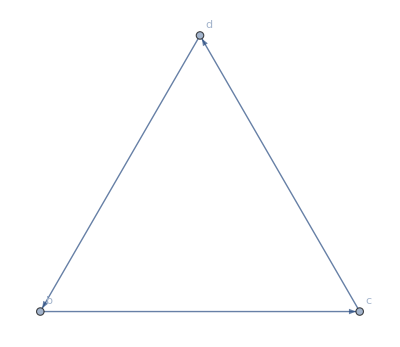

```mathematica
graph=Graph[{b->c,c->d,d->b},VertexLabels->Automatic]
```

```mathematica
Unbalance[Graph[{b->c,c->d,d->b}],b]
```

-2

```mathematica
VertexDegree[graph,b]
```

2

```mathematica
IncidenceList[graph,b]
```

{b->c,d->b}

```mathematica
ClearAll[Unbalance]
Unbalance[g_?GraphQ,v_]:=Block[{incidenceList},incidenceList=IncidenceList[g,v];
Length[Cases[incidenceList,v->_]]-Length[Cases[incidenceList,_->v]]-Length[Cases[incidenceList,_<->v]]-Length[Cases[incidenceList,v<->_]]]
```

```mathematica
ClearAll[UnbalanceList]
UnbalanceList[g_?GraphQ,v_]:=Block[{incidenceList},incidenceList=IncidenceList[g,v];
{Cases[incidenceList,v->_],Cases[incidenceList,_->v],Join[Cases[incidenceList,_<->v],Cases[incidenceList,v<->_]]}]
```

```mathematica
Unbalance[graph,b]
```

0

```mathematica
Cases[IncidenceList[graph,b],b_->_]
```

{b->c,d->b}

```mathematica
Cases[IncidenceList[graph,b],_->b]
```

{d->b}

```mathematica
Cases[IncidenceList[graph,b],b<->_]
```

{}

```mathematica
Cases[IncidenceList[graph,b],_<->b]
```

{}

```mathematica
graph
```

-Graphics-

```mathematica
Unbalance[graph,b]
```

0

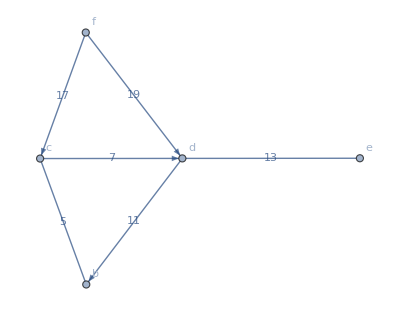

```mathematica
graph=Graph[{Annotation[b<->c,EdgeWeight->Prime[3]],Annotation[c->d,EdgeWeight->Prime[4]],Annotation[d->b,EdgeWeight->Prime[5]],Annotation[d<->e,EdgeWeight->Prime[6]],Annotation[f->c,EdgeWeight->Prime[7]],Annotation[f->d,EdgeWeight->Prime[8]]},VertexLabels->Automatic,EdgeLabels->"EdgeWeight"]
```

```mathematica
Unbalance[graph,d]
```

-2

```mathematica
1-2-1
```

-2

```mathematica
Odd[g_?GraphQ,v_]:=Boole@OddQ[VertexDegree[g,v]]
```

```mathematica
Odd[graph,d]
```

0

```mathematica
VertexDegree[graph,d]
```

4

```mathematica
WeightedAdjacencyMatrix[graph]//MatrixForm
```

(0 | 5 | 11 | 0 | 0
5 | 0 | 7 | 0 | 0
11 | 0 | 0 | 13 | 0
0 | 0 | 13 | 0 | 0
0 | 17 | 19 | 0 | 0)

```mathematica
IncidenceList[graph,d]
```

{c->d,d<->b,d<->e,f->d}

```mathematica
UnbalanceList[graph,d]
```

{{d->b},{c->d,f->d},{d<->e}}

```mathematica
Unbalance[graph,d]
```

-2

```mathematica
UnbalanceList[graph,b]
```

{{},{d->b},{b<->c}}

```mathematica
Odd[graph,b]
```

0

```mathematica
UnbalanceList[graph,c]
```

{{c->d},{f->c},{b<->c}}

```mathematica
UnbalanceList[graph,f]
```

{{f->c,f->d},{},{}}

```mathematica
UnbalanceList[graph,e]
```

{{},{},{d<->e}}